The conclusion of this experiment is 
that Zykov only works for complete graphs.

```mathematica
FindEmptyFormula2[g_]:=Block[{},
Monitor[
formulaDepth=0;Simplify[FindEmptyFormula2[g,Table[{v},{v,VertexList[g]}]]],
formulaDepth
]
]
```

```mathematica
FindEmptyFormula2[g_,v_]:=Block[{edge,pos1,pos2,v2,result={}},
If[EmptyGraphQ[g],
(* ok : done *)
result=SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&],"n"]
,
(* else *)
edge=First[EdgeList[g]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=FindEmptyFormula2[EdgeDelete[g,edge],v]-
FindEmptyFormula2[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
MakeEmpty[g_,vertices_]:=Block[{result=g},
Table[
If[EdgeQ[result,fromto],
result=EdgeDelete[result,fromto]
],
{fromto,Map[#[[1]]<->#[[2]]&,Subsets[vertices,{2}]]}
];
Graph[VertexList[result],EdgeList[result],VertexLabels->"Name"]
]
```

```mathematica
ZykovDecompositionEmpty[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sol,lefta,middlea,righta, formula, symbols, coeff},
split= ConnectedComponents[VertexDelete[g,vertices]];
If[Length[split ]!= 2,Throw["Vertices don't split the graph in 2 "];  Interrupt[]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeEmpty[left,vertices];
right2=MakeEmpty[right,vertices];
middle2=MakeEmpty[middle,vertices];
formula=FindEmptyFormula2[middle];
symbols=ListofVars[formula];
Monitor[
Column[
{GraphWithChrom[Graph[EdgeList[g],GraphHighlight->VertexList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
TableForm[
Table[
sol= SymbolToSets[symbol];
coeff=Coefficient[formula,symbol];
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->VertexList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->VertexList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
With[{chrom=Simplify[(ChromaticPolynomial[lefta,x]*ChromaticPolynomial[righta,x]/ChromaticPolynomial[middlea,x])]},
{Rotate[Labeled[SetsToLabel[sol],{coeff,(coeff*chrom/.x->4)}],Pi/2],GraphWithChrom[lefta],GraphWithChrom[righta],GraphWithChrom[middlea],Rotate[Framed[Factor[chrom/(x(x-1))]],-Pi/2]}
],
{symbol,symbols}
]
]
}
],
sol]
]
```

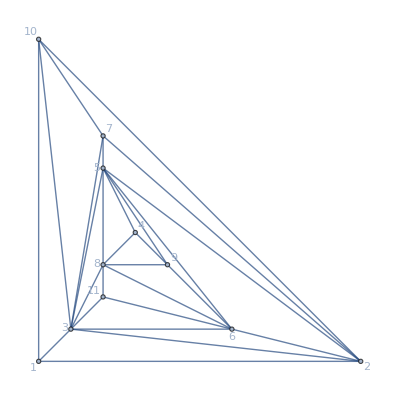

```mathematica
g=Graph[ReadGrof[1000],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

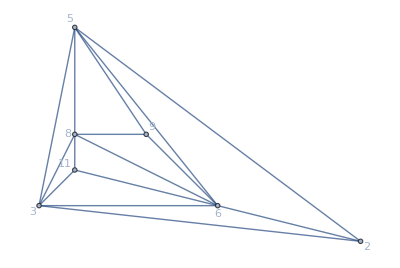

```mathematica
NeighborhoodGraph[g,6]
```

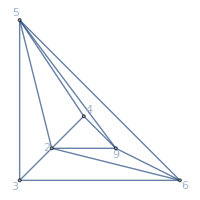
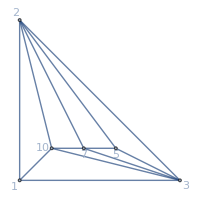
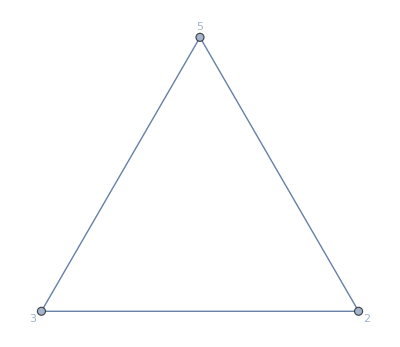
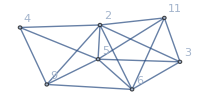
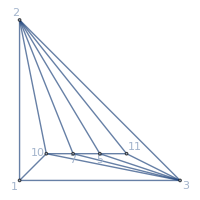
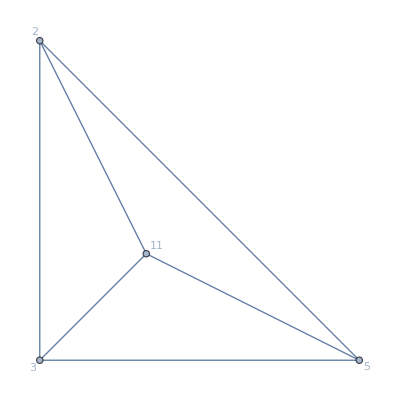
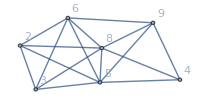
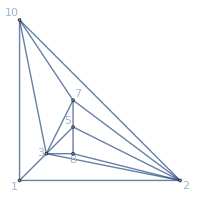
-Graphics-{(-3+x)^8 (-2+x),24}
28♁3♁5b24 | -Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{(-3+x)^3 (-2+x),24} | -Graphics-{-2+x,24} | (-3+x)^6 (-2+x)
28♁3♁5♁b0 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x),24} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x)^6 (-2+x)
2♁3♁5b♁80 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x),24} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x)^6 (-2+x)
2b♁3♁5♁80 | -Graphics-{(-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-3+x)^4 (-2+x),24} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x)^6 (-2+x)
2♁3♁5♁8♁b0 | -Graphics-{(-5+x) (-4+x) (-3+x)^3 (-2+x),0} | -Graphics-{(-4+x) (-3+x)^4 (-2+x),0} | -Graphics-{(-4+x) (-3+x) (-2+x),0} | (-5+x) (-4+x) (-3+x)^6 (-2+x)

```mathematica
ZykovDecomposition[g,{2,3,11,8,5}]
```